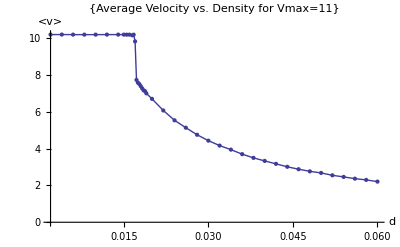

```mathematica
vbar11=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vbar.vmax11.txt",{Number,Number}];
a=ListPlot[vbar11,PlotLabel->{"Average Velocity vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full];
b=ListLinePlot[vbar11,PlotLabel->{"Average Velocity vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a,b]
```

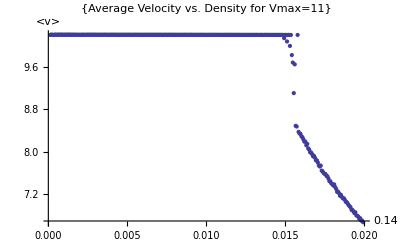

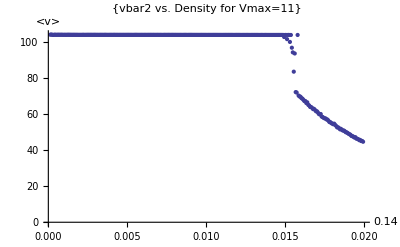

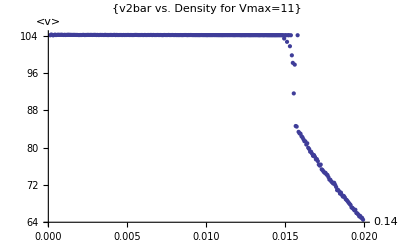

```mathematica
vbar=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/vbar.vmax11.fine4.txt",{Number,Number}];
vbar2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/vbar2.vmax11.fine4.txt",{Number,Number}];
v2bar=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/v2bar.vmax11.fine4.txt",{Number,Number}];
vbarf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/vbar.vmax11.fine5.txt",{Number,Number}];
vbar2f=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/vbar2.vmax11.fine5.txt",{Number,Number}];
v2barf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vmax11/v2bar.vmax11.fine5.txt",{Number,Number}];
a2=ListPlot[vbar,PlotLabel->{"Average Velocity vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full];
b2=ListLinePlot[vbar,PlotLabel->{"Average Velocity vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full];
Show[a2]
ListPlot[vbar2,PlotLabel->{"vbar2 vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full]
ListPlot[v2bar,PlotLabel->{"v2bar vs. Density for Vmax=11"},AxesLabel->{d,"<v>"},PlotRange->Full]
```

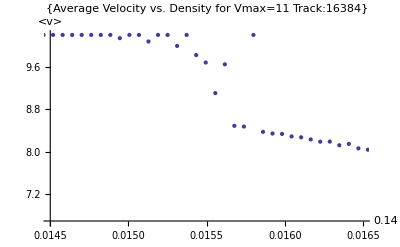

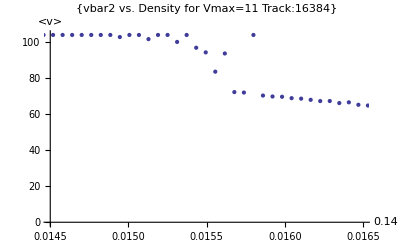

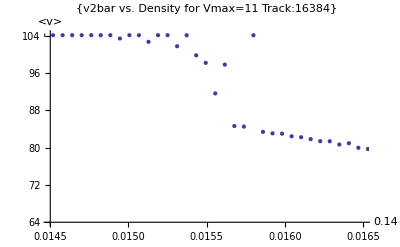

```mathematica
ListPlot[vbar,PlotLabel->{"Average Velocity vs. Density for Vmax=11  Track:16384"},AxesLabel->{d,"<v>"},PlotRange->{{0.0145,0.0165},Full}]
ListPlot[vbar2,PlotLabel->{"vbar2 vs. Density for Vmax=11  Track:16384"},AxesLabel->{d,"<v>"},PlotRange->{{0.0145,0.0165},Full}]
ListPlot[v2bar,PlotLabel->{"v2bar vs. Density for Vmax=11  Track:16384"},AxesLabel->{d,"<v>"},PlotRange->{{0.0145,0.0165},Full}]
```

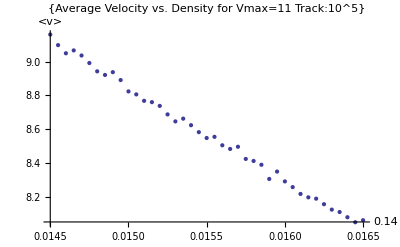

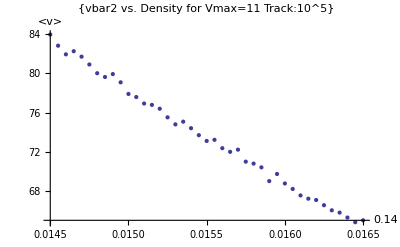

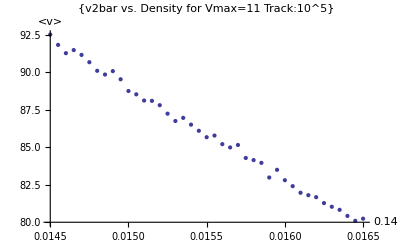

```mathematica
ListPlot[vbarf,PlotLabel->{"Average Velocity vs. Density for Vmax=11  Track:10^5"},AxesLabel->{d,"<v>"},PlotRange->Full]
ListPlot[vbar2f,PlotLabel->{"vbar2 vs. Density for Vmax=11  Track:10^5"},AxesLabel->{d,"<v>"},PlotRange->Full]
ListPlot[v2barf,PlotLabel->{"v2bar vs. Density for Vmax=11  Track:10^5"},AxesLabel->{d,"<v>"},PlotRange->Full]
```

16384. = L

32 = N

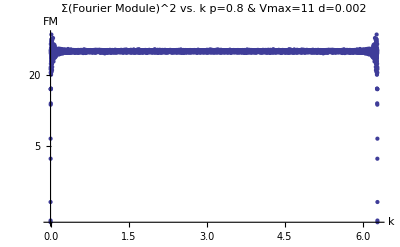

31.9394 = N*(L-N)/(L-1)

32.1936 = Mean of o.7 largest values

523264. = Sum of All L-1 Valus

523264. = N*(L-N)

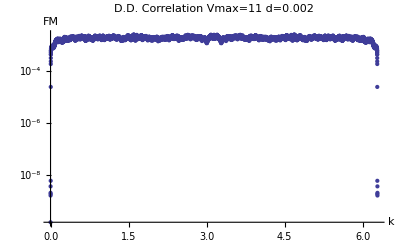

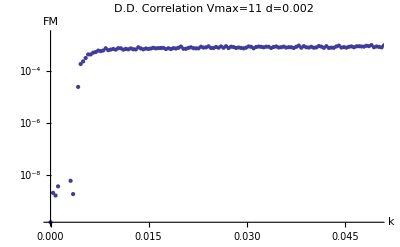

0.00189221 = (N-1)/(L-1)

0.00195562 = Mean of o.9 largest values

31. = Sum of All L Valus

31 = N-1

Values lesser than 2/3*(N-1)/(L-1):

{0,1.52588×10^-10}

{1,2.07382×10^-9}

{2,1.63596×10^-9}

{3,3.68019×10^-9}

{4,-9.71176×10^-9}

{5,-5.72959×10^-9}

{6,-3.82225×10^-9}

{7,-1.18436×10^-9}

{8,6.04225×10^-9}

{9,1.85877×10^-9}

{10,-3.30859×10^-9}

{11,0.000025003}

{12,0.000190625}

{13,0.000240617}

{14,0.000325}

{15,0.000446865}

{16,0.000446875}

{17,0.000521873}

{18,0.00055313}

{19,0.000628116}

{20,0.000600009}

{21,0.000634368}

{22,0.000768756}

{23,0.000650002}

{24,0.000687497}

{25,0.000725002}

{26,0.000684385}

{27,0.000781243}

{28,0.000771875}

{29,0.000684379}

{30,0.000731249}

{31,0.000703117}

{32,0.000762501}

{33,0.000709373}

{34,0.000696873}

{35,0.000840631}

{36,0.000762503}

{37,0.000703125}

{38,0.000756242}

{39,0.000728133}

{40,0.000756257}

{41,0.000803118}

{42,0.000765629}

{43,0.000781255}

{44,0.000790622}

{45,0.000799997}

{46,0.000721868}

{47,0.000775008}

{48,0.000721862}

```mathematica
d="0.002";
n=16384.000;
a="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vvmax11/fourier.1d.averaged.d";
b=".p0.8.v11.txt";
g=".p0.8.v11.txt";
c=a<>d<>b;
e="/Users/ashkanbalouchi/Desktop/Traffic/Trafficsim/FFT-Analyse/bit/results/vvmax11/ddensitycorrelation.d";
f=e<>d<>g;
j=StringToStream[d];
o= Read[j,Number];
m=Floor[o*16384];
n "= L"
m  "= N  "
bitF=ReadList[c,{Number,Number}];
bitf2=bitF[[All,2]];
ListLogPlot[bitF,PlotLabel->"Σ(Fourier Module)^2 vs. k  p=0.8 & Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
(n-m)*m/(n-1) "= N*(L-N)/(L-1)"
TrimmedMean[bitf2,{0.3,0}] "= Mean of o.7 largest values"
summ=Sum[bitf2[[i]],{i,1,n-1} ];
N[summ] "= Sum of All L-1 Valus"
m*(n-m) "= N*(L-N)"
Δ=summ-m*(n-m);
density=ReadList[f,{Number,Number}];
density2=density[[All,2]];
ListLogPlot[density,PlotLabel->"D.D. Correlation Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->Full]
ListLogPlot[density,PlotLabel->"D.D. Correlation Vmax=11 d="<>  d,AxesLabel->{k,FM},PlotRange->{{0,0.05},Full}]
p=(m-1)/(n-1);
p  "= (N-1)/(L-1)"
TrimmedMean[density2,{0.1,0}] "= Mean of o.9 largest values"
summ2=Sum[density2[[i]],{i,1,n} ];
N[summ2] "= Sum of All L Valus"
m2=m-1;  
m2 "= N-1"
"Values lesser than 2/3*(N-1)/(L-1):"
For[i=0,i<50,i++,
If[density2[[i]]<2*p/3,
Print[{i-1,density2[[i]]}]
]
]
```